```mathematica
Exit[];
```

```mathematica
$Assumptions=  r>0 && Element[m,Integers] && Element[n,Integers]  && s>0
```

r>0&&m∈Integers&&n∈Integers&&s>0

# 2-d Dirac

```mathematica
f1[r_,En_]:={{(m-1)/r,I*(En-r^p)},{I*(En-r^p),-m/r}};f1[r,En]//MatrixForm
```

((-1+m)/r | ⅈ (En-r^p)
ⅈ (En-r^p) | -m/r)

# Diagonaldarstellung für r gegen Infinity

```mathematica
V={{1,1},{-1,1}};Simplify[V.f1[r,En].Inverse[V]]//MatrixForm
```

(ⅈ En-1/(2 r)-ⅈ r^p | (1-2 m)/(2 r)
(1-2 m)/(2 r) | -ⅈ En-1/(2 r)+ⅈ r^p)

```mathematica
Inverse[V].{0,C}
```

{-C/2,C/2}

# Potenzreihenansatz mit richtigem Rangverhalten

# m>=1

```mathematica
s=m-1;p=.;
```

```mathematica
f1[r,En]//MatrixForm
```

((-1+m)/r | ⅈ (En-r^p)
ⅈ (En-r^p) | -m/r)

```mathematica
u={F[x],G[x]}*x^(s)
```

{x^(-1+m) F[x],x^(-1+m) G[x]}

```mathematica
r[x_]:=x;
```

```mathematica
g1=Collect[Expand[Simplify[Expand[-(D[u,x]-r'[x]*f1[r[x],En].u)/x^(s-0)]]],{x^n,a[n],b[n],F[x],G[x]}];
g1
```

{(ⅈ En-ⅈ x^p) G[x]-F'[x],(ⅈ En-ⅈ x^p) F[x]+(1/x-(2 m)/x) G[x]-G'[x]}

```mathematica
m=.;
```

```mathematica
f2[x_,En_]:={{0,(ⅈ En-ⅈ x^p) },{(ⅈ En-ⅈ x^p),(1/x-(2 m)/x) }};f2[r,En]//MatrixForm
```

(0 | ⅈ En-ⅈ r^2
ⅈ En-ⅈ r^2 | 1/r-(2 m)/r)

```mathematica
u={F[x],G[x]}*Exp[I*(x^(p+1)/(p+1)-x*En)]
```

{ⅇ^(ⅈ (-En x+x^(1+p)/(1+p))) F[x],ⅇ^(ⅈ (-En x+x^(1+p)/(1+p))) G[x]}

```mathematica
g1=Collect[Expand[Simplify[Expand[-(D[u,x]-r'[x]*f2[r[x],En].u)/Exp[I*(x^(p+1)/(p+1)-x*En)]]]],{x^n,a[n],b[n],F[x],G[x]}];
g1
```

{(ⅈ En-ⅈ x^p) F[x]+(ⅈ En-ⅈ x^p) G[x]-F'[x],(ⅈ En-ⅈ x^p) F[x]+(ⅈ En+1/x-(2 m)/x-ⅈ x^p) G[x]-G'[x]}

```mathematica
f[x_,En_]:={{(ⅈ En-ⅈ x^p) ,(ⅈ En-ⅈ x^p) },{(ⅈ En-ⅈ x^p),(ⅈ En+1/x-(2 m)/x-ⅈ x^p) }};f[r,En]//MatrixForm
```

(ⅈ En-ⅈ r^p | ⅈ En-ⅈ r^p
ⅈ En-ⅈ r^p | ⅈ En+1/r-(2 m)/r-ⅈ r^p)

```mathematica
Expand[V.f[r,En].Inverse[V]]//MatrixForm
```

(2 ⅈ En+1/(2 r)-m/r-2 ⅈ r^p | 1/(2 r)-m/r
1/(2 r)-m/r | 1/(2 r)-m/r)

```mathematica
Inverse[V].{EE,C}
```

{-C/2+EE/2,C/2+EE/2}

```mathematica
u={a[n],b[n]}*x^n
```

{x^n a[n],x^n b[n]}

```mathematica
p=2;
```

```mathematica
r[x_]:=x;
```

```mathematica
g1=Collect[Expand[Simplify[Expand[-(D[u,x]-r'[x]*f[r[x],En].u)*x]]],{x^n,a[n],b[n],F[x],G[x]}];
g1
```

{x^n ((-n+ⅈ En x-ⅈ x^3) a[n]+(ⅈ En x-ⅈ x^3) b[n]),x^n ((ⅈ En x-ⅈ x^3) a[n]+(1-2 m-n+ⅈ En x-ⅈ x^3) b[n])}

```mathematica
g2=Table[Simplify[Sum[D[g1,{x,n2}]/n2!,{n,0,7}]/.x->0],{n2,0,7}];g2//MatrixForm
```

(0 | 0
0 | 0
0 | 0
0 | 0
0 | 0
0 | 0
0 | 0
0 | 0)

```mathematica
a[0]=1;b[0]=0; a[1]=I*En;a[2]=I En (a[1]+b[1])/2;
```

```mathematica
a[1]=.;a[2]=.;b[1]=.;b[0]=.;a[0]=.;b[2]=.;a[n_]=.;b[n_]=.;
```

Unset::norep: Assignment on b for b[1] not found.

Unset::norep: Assignment on b for b[2] not found.

```mathematica
b[n_]:=n/(-1+2 m+n)a[n];
```

```mathematica
a[n_]:=ⅈ (En a[n-1] (2 m -1 +2 (n-1))/(n(2 m-1+(n-1)))-a[n-3](2m-1+2(n-3))/(n(2m-1+(n-3))))
```

```mathematica
Simplify[((2 m -1 +2 (n-1))/(n(2 m-1+(n-1)))/.n->n+1)/((2 m -1 +2 (n-1))/(n(2 m-1+(n-1))))]
```

(n (-2+2 m+n) (-1+2 m+2 n))/((1+n) (-1+2 m+n) (-3+2 m+2 n))

```mathematica
Solve[ⅈ (En  FF[n-1]-X^2FF[n-3])-X==0,X]
```

{{X→(ⅈ-√(-1+4 En FF[-3+n] FF[-1+n]))/(2 FF[-3+n])},{X→(ⅈ+√(-1+4 En FF[-3+n] FF[-1+n]))/(2 FF[-3+n])}}

```mathematica
Un[Ene_,mm_,nN_,x_]:=Module[{n,U1,U2,U3,U4,Erg},
U1={a[0],b[0]};U2={a[1],b[1]};U3={a[2],b[2]};
Erg=U1+U2*x+U3*x^2;
For[n=3,n≤nN,n++,
U4=Simplify[{1/n ⅈ (Ene U3[[2]]-U1[[1]]-U1[[2]]),I/(n-1+2 mm)* (Ene U3[[1]]-U1[[1]]-U1[[2]])}]//N;
U1=U2;U2=U3;U3=U4;
Erg+=U3*x^n;

];

Erg]
```

# zur Probe

```mathematica
Uno[Ene_,m_,nN_,x_]:=Module[{n,U,Erg=0},
U={{a[0],b[0]}};
For[n=1,n≤nN+1,n++,
AppendTo[U,{a[n],b[n]}]
];
For[n=0,n≤nN,n++,
Erg+=U[[n+1]]*x^n;
];
Erg
]
```

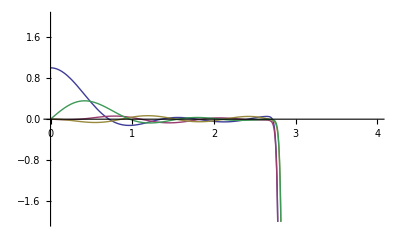

```mathematica
Ge={Re[#],Im[#]}&[Un[En,m,150,x]];Plot[Ge,{x,0,4},PlotRange->{-2,2}]
```

```mathematica
Analytische Lösung an stelle x mit güte g
```

```mathematica
U[Ene_,mm_,g_,x_]:=Module[{n=2,U1,U2,U3,U4,Erg},
U1={a[0],b[0]};U2={a[1],b[1]};U3={a[2],b[2]};
Erg=U1+U2*x+U3*x^2;
While[Sqrt[Abs[U3.Conjugate[U3]*x^(2n)]]>g,n++;
U4=Simplify[{1/n ⅈ (Ene U3[[2]]-U1[[1]]-U1[[2]]),I/(n-1+2 mm)* (Ene U3[[1]]-U1[[1]]-U1[[2]])}]//N;
U1=U2;U2=U3;U3=U4;
Erg+=U3*x^n;

];

{Erg,n}]
```

```mathematica
U[5.533021207627789+0.2865166733657229 ⅈ,2,10^-10,1]
```

{{-0.119165+0.0406181 ⅈ,0.030514-0.0178352 ⅈ},44}

# Berechnung der Eigenwerte

```mathematica
f3[rr_,Ennn_]=V.f[rr,Ennn].Inverse[V];f[erd,Ens]//MatrixForm
```

(-ⅈ erd^2 | ⅈ Ens-ⅈ erd^2
ⅈ Ens-ⅈ erd^2 | -3/erd-ⅈ erd^2)

```mathematica
nn=5000;S=1;h=10/nn;ra=1;En=8.64233766468516+0.18101616081185867 ⅈ;m=2;r=1;
NN=U[En,m,10^-10,r];NN[[2]]
k=V.NN[[1]];
kK={{r,k}};
Do[
k0=h*f3[r,En].k;k1=h*f3[r+h/2,En].(k+k0/2);k2=h*f3[r+h/2,En].(k+k1/2);k3=h*f3[r+h,En].(k+k2);
k+=1/6*(k0+2*k1+2*k2+k3);r+=h;
AppendTo[kK,{r,k}],{nn}];

ListPlot[Join[{ {#[[1]],Re[#[[2,1]]]}&/@kK[[S;;nn]]//N},{ {#[[1]],Im[#[[2,1]]]}&/@kK[[S;;nn]]//N}],PlotRange->All,Joined->True]
ListPlot[Join[{ {#[[1]],Re[#[[2,2]]]}&/@kK[[S;;nn]]//N},{ {#[[1]],Im[#[[2,2]]]}&/@kK[[S;;nn]]//N}],PlotRange->All,Joined->True]
r=.;
```

2

$Aborted

$Aborted

$Aborted

```mathematica
f[r,En]
```

{{-ⅈ x^2,(-0.286517+5.53302 ⅈ)-ⅈ x^2},{(-0.286517+5.53302 ⅈ)-ⅈ x^2,-3/x-ⅈ x^2}}

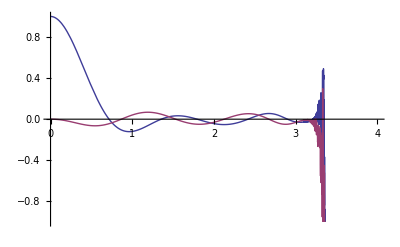

```mathematica
Ge={Re[#],Im[#]}&[Un[En,2,250,x][[1]]];Plot[Ge,{x,0,4},PlotRange->{-1,1}]
```